```mathematica
∫_0^(+∞) (cos(x ω))/(ω^2+1)ⅆω
```

```mathematica
ConditionalExpression[1/2 ⅇ^(-Abs[x]) π, x∈Reals]
Subscript[ℱ, ω][exp(1/2 (-a) x^2)](x)
```

ConditionalExpression[1/2 ⅇ^(-Abs[x]) π, x∈ℝ]

FourierTransform[ⅇ^(-(a x^2)/2),ω,x]

```mathematica
∫_0^π (cos(x))/(θ cos(x)+1)ⅆx
```

ConditionalExpression[(π (-1+θ+√(-1+2/(1+θ))))/((-1+θ) θ), Re[ArcSec[θ]]<0||Re[ArcSec[-θ]]<0||ArcCsc[θ]∉ℝ]

```mathematica
ClearAll
N[Beta[3/4,1/2]]
```

ClearAll

2.39628

```mathematica
Gamma[3]
```

2

```mathematica
∫_y^(y^2) x^2 exp(-x^2 y)ⅆx
```

```mathematica
1/4 (2 ⅇ^(-y^3)-2 ⅇ^(-y^5) y+(√π (-Erf[y^(3/2)]+Erf[y^(5/2)]))/y^(3/2))
```

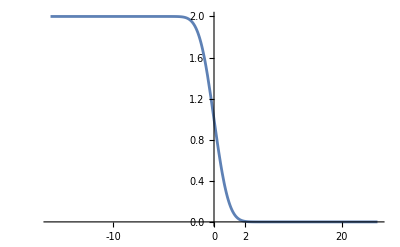

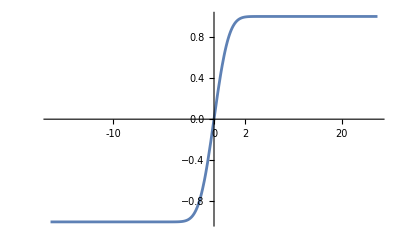

```mathematica
Plot[Erfc[x],{x,-Infinity,+Infinity}]
Plot[Integrate[2 Exp[-t^2]/Sqrt[Pi],{t,0,x}],{x,-Infinity,+Infinity}]
```

```mathematica
∫y exp(-x y)ⅆy
```

-(ⅇ^(-x y) (1+x y))/x^2

```mathematica
∫_ϵ^∞ 2/(x^2+1)ⅆxϵ0-1+
```

π

```mathematica
|-1|
```

```mathematica
f[0]=0;
f[x_]=f[x-1]+x;
f[100]
```

394+TerminatedEvaluation[RecursionLimit]

```mathematica
3+TerminatedEvaluation["RecursionLimit"]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Factor[x^3+x^2-x]
```

x (-1+x+x^2)

```mathematica
f[x_]=Exp[2x];
Solve[∫_a^b f(x)ⅆx==f(a) (ϵ-a)+f(b) (b-ϵ),ϵ]
```

{{ϵ→(-ⅇ^(2 a)+2 a ⅇ^(2 a)+ⅇ^(2 b)-2 b ⅇ^(2 b))/(2 (ⅇ^(2 a)-ⅇ^(2 b)))}}

```mathematica
NIntegrate[x ArcTan[x]/(1+x^3),{x,1,+Infinity}]
```

0.980062

```mathematica
NIntegrate[Sin[x]/x,{x,1,+Infinity}]
```

0.624713

```mathematica
Plot[N[Sum[Sin[n x],{n,0,100}]],{x,0,2 Pi}]
```

Sum::div: Sum（和）不收敛.

NIntegrate::deorel: 在 DoubleExponentialOscillatory 方法下，对于被积函数 0.00192535 Cos[0.000128356 n]，调整参数 TuningParameters -> {10,5}，在 {0,∞} 上，相对误差 7.42479×10^7 大于期望值.

NIntegrate::deoncon: 在 {0,∞} 上，对于被积函数 0.00192535 Cos[0.000128356 n]，DoubleExponentialOscillatory 无法收敛. 对于积分和误差估计，DoubleExponentialOscillatory 得到 -1.87388×10^-6 和 7.42479×10^8.

NIntegrate::ncvb: 在接近 {n} = {6.3887×10^56} 处的 n 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -9.42143×10^243 和 9.2865×10^243.

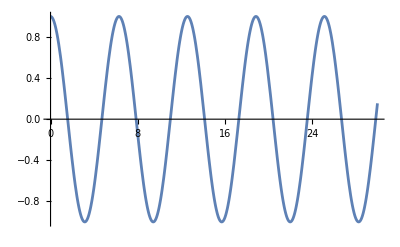

```mathematica
Plot[Sum[(x)^(2n)*(-1)^n/(2n)!,{n,0,+Infinity}],{x,0,+30}]
```

```mathematica
ClearAll;
(1)y1(x_,t_)=Acos(tω-(2πvx)/u);
(2)y2(x_,t_)=Acos(tω+(2πvx)/u+π);    X={(3 u)/(4 v),u/(4 v)}
Solve[y1[x,t]==y2[x,t],x]
```

Set::setraw: 无法赋值给原始对象 2.

{(3 u)/(4 v),u/(4 v)}

Solve::ivar: (3 u)/(4 v) 不是一个有效的变量.

Solve[True,{(3 u)/(4 v),u/(4 v)}]

```mathematica
Plot[N[((-1)^n x^(1+2 n))/((1+2 n)!)n0∞],{x,0,2Pi}]
Series[Sin[x],{x,0,30}]
```

-Graphics-

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000+x^21/51090942171709440000-x^23/25852016738884976640000+x^25/15511210043330985984000000-x^27/10888869450418352160768000000+x^29/8841761993739701954543616000000+O[x]^31

```mathematica
Asymptotic[Sin[x],{x,0,∞}]
```

((-1)^n x^(1+2 n))/((1+2 n)!)n0∞

```mathematica
Subscript[n, 1]=Abs[(1.62-1.50)/(1.62+1.50)]
Subscript[n, 2]=Abs[(1.62-1.75)/(1.75+1.62)]
```

0.0384615

0.0385757

```mathematica
FourierTransform[Abs[Sin[x]],x,ω]
```

∑_(K[1]=-∞)^∞ -(4 √(2/π) (1+(-1)^K[1]+2 Cos[1/2 π K[1]]) DiracDelta[2 ω+K[1]])/(-4+K[1]^2)

```mathematica
Manipulate[Simplify[1/2^n/n! D[(1-x^2)^n,{x,n}]],{n,1,10}]
```

```mathematica
Integrate[D[(1-x^2)^1,{x,1}] D[(1-x^2)^3,{x,3}],{x,-1,1}]
```

0

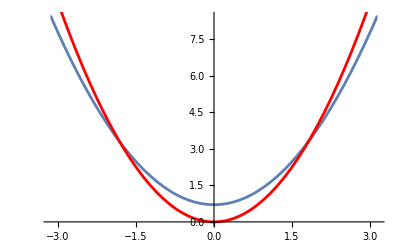

```mathematica
y=Plot[Sum[(-1)^n  Pi/n^2 Cos[n x],{n,1,100}]+ Pi^2/3,{x,-Pi,Pi}];
z=Plot[x^2,{x,-Pi,Pi},PlotStyle->Red];
Show[y,z]
```

```mathematica
Integrate[x^2,{x,-Pi,Pi}]
```

(2 π^3)/3

```mathematica
FourierCosSeries[x^2,x,Infinity]
```

π^2/3+2 (2-ⅇ^(-ⅈ x)+2-ⅇ^(ⅈ x))

```mathematica
f[n,4]
f[n,2]
```

(2 n Sin[n π])/(-16+n^2)

(2 n Sin[n π])/(-4+n^2)

```mathematica
n
```

```mathematica
ClearAll;
f[m_Integer,n_Integer]=Integrate[Cos [n x] Cos[m x],{x,-Pi,Pi}];
Manipulate[3/8 f[0,n]+f[4,n]/8-f[2,n]/2,{n,0,10}]
```

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0 ComplexInfinity.

```mathematica
500/2/1.38/2
```

90.5797

```mathematica
500/1.6/4
```

78.125

```mathematica
0.25*Tan[10^-4]*2
```

0.00005

```mathematica
0.25*Tan[10^-4]*2*10^7
```

```mathematica
500.0000016666667
N[Tan[90]]
```

500.

-1.9952

```mathematica
{亮,λ/2/Subscript[n, 2]}
```

{亮,λ/(2 n_2)}

```mathematica
θ=12*500*10^-9/(0.25*10^-3/(500*10^-9))
```

1.2×10^-8

```mathematica
12*10^-3/θ
```

1.×10^6

```mathematica
2.3999999999999995*^6
```

2.4×10^6

3*598*10^-9/(0.4*10^-4)

0.04485

```mathematica
3*598*10^-9/(0.4*10^-3)/3*2
```

0.00299

```mathematica
1.44/400
```

0.0036